1

0.01

1

0.01 (-ⅇ^(-2 t)+4 ⅇ^-t+2 t)

10

0.2

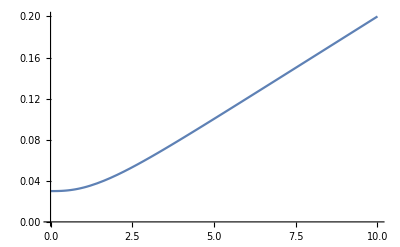

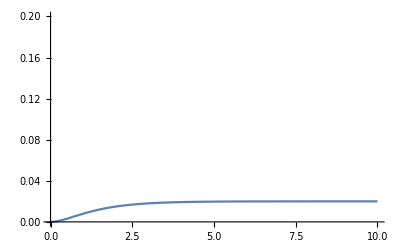

```mathematica
vo = 1
d = 0.01
α = 1
β[t_]=(vo^2 d)/α^3(2 α t - Exp[-2 α t] + 4 Exp[-α t])
xmax = 10
ymax = 0.2
Plot[β[t],{t,0,xmax},PlotRange->{{0,xmax},{0,ymax}}]
Plot[Evaluate[D[β[t],t]],{t,0,xmax},PlotRange->{{0,xmax},{0,ymax}}]
(*Plot[β[t],{t,0,xmax},PlotRange->All]*)
```